```mathematica
ClearAll["Global`*"]
```

```mathematica
ClearAll[Ω,Δ, tfinal, μ]
```

```mathematica
ClearAll[Ω,Δ,θ]
```

```mathematica
ClearAll[φ]
```

```mathematica
σz=PauliMatrix[3];
σx=PauliMatrix[1];
σy=PauliMatrix[2];
```

```mathematica
Element[μ[t],Complexes];
Element[μ'[t],Complexes];
Element[Ω[t], Reals];
Element[Δ[t],Reals];
Element[θ[t],Complexes];
Element[θ'[t],Complexes];
Element[Γ, Reals];
Element[θr[t],Reals];
Element[θi[t],Reals];
```

```mathematica
p=2
(*Arbitrary bound for the above fucntions a, b and μ*)
```

2

```mathematica
aCoefficients=Table[Subscript[A,n],{n,0,p}];
bCoefficients=Table[Subscript[B,n],{n,0,p}];
cCoefficients=Table[Subscript[Y,m],{m,0,p}];
dCoefficients=Table[Subscript[Z,m],{m,0,p}];
```

```mathematica
(*Define the Fourier coefficients as symbols*)
aCoefficients=Table[Symbol["A"<>ToString[n]],{n,0,p}];
bCoefficients=Table[Symbol["B"<>ToString[n]],{n,0,p}];
(*Define the frequency as a symbol*)
λA[n_]:=(2 n π)/tfinal;

(*Define the Fourier series function a[t]*)
a[t_]:=Sum[(aCoefficients[[n]]+aCoefficients[[n+1]](1- Cos[λA[n] t]))+bCoefficients[[n]] Sin[λA[n] t],{n,1,p}]

(*Define the Fourier coefficients as symbols*)
cCoefficients=Table[Symbol["Y"<>ToString[m]],{m,0,p}];
dCoefficients=Table[Symbol["Z"<>ToString[m]],{m,0,p}];
(*Define the frequency as a symbol*)
λB[m_]:=(2 m π)/tfinal;

(*Define the Fourier series function a[t]*)
b[t_]:=Sum[cCoefficients[[m]]+(cCoefficients[[m+1]](1- Cos[λB[m] t]))+dCoefficients[[m]] Sin[λB[m] t],{m,1,p}]
 
μ[t_]:=a[t]+ⅈ b[t]

(*SO the tweak i made was instead of Sum(An(1-cos(λt)+BnSin(λt)), I made it Sum(An+An+1(1-cos(λt)+BnSin(λt))
Logic being if this thing has some sort of discontinuity i should add an aribtrary phase shift.

If unclear, notitce how cCoefficients and aCoefficients represent our intial phase shift term, well above they've been assigned symbolically as Y's and A's respectively, so An and Yn will always come from the cos part.  )*)
```

```mathematica
μ[tfinal]
(*this is the phase shift being left over, so if this quanity must equal zero, then A0-A3=-ⅈ (Y0-Y3), while this may seem trivial, its what repairs the discontinuity in the out put of Iz[0] or Ix[0], more will be said further below. 
note it might be 2or3 for coefficient terms idrk doesn't really matter quite literally. just focus on the relation in the explanantion below*)
```

A0+A1+ⅈ (Y0+Y1)

```mathematica
(*t∈ Interval[{0,tfinal},{1,-1}]*)
```

```mathematica
(*θ[t_]:=-ArcTan[Ω[t]/(Δ[t]+ⅈ/2 Γ)]*)
θ[t_]:=θr[t]+I θi[t]
Simplify[Im[θ[t]],Assumptions->{θr[t]∈Reals,θi[t]∈Reals}]
CO
(*You know what da ting is*)
```

θi[t]

Im[θr[t]]+Re[θi[t]]

```mathematica
(*θ[t_]:=2ArcTan[(-(Ω[t]/(√((Δ[t] + ⅈ Γ/2)^2+Ω[t]^2)+Δ[t]+ ⅈ Γ/2)))]*)
```

```mathematica
Δ[t_]:=Δ0 Sin[2 π t+φ];
Ω[t_]:=Ω0 + Δ0 Cos[2π t+φ];
(*φ=π/2*)
(*Once Functions gxmod and gzmod have been ComplexExpanded and set ,equal to Ix and Iz, and evaluated at t=0, set phi here to π/2, reason being if you look carefully it will killoff many sin terms,now this may not be the best selction but at the time it was the obvious parameter value I saw.*)
```

```mathematica
Γ=1;
Δ0=1/2;
Ω0=1/2;
φ=0;
```

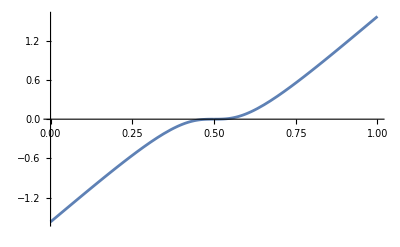

```mathematica
Plot[Re[θ[t]],{t,0,1}]
```

```mathematica
gzmod[t_]:=-(ⅈ Γ)/2-Δ[t]+1/2(θ'[t] Cot[μ[t]] Sin[θ[t]])+1/2(μ'[t] Cos[θ[t]])
gxmod[t_]:=1/2 (-2 Ω[t]+Cot[μ[t]] Sin[θ[t]] θ'[t]+Cos[θ[t]] μ'[t])
```

```mathematica
Refine[μ[t],{Element[a[t],Reals], Element[b[t],Reals]}]
(*Honestly I don't think there's any reason to execute this cell but I would jsut do it*)
```

A0+A1+A1 (1-Cos[(2 π t)/tfinal])+A2 (1-Cos[(4 π t)/tfinal])+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal]+ⅈ (Y0+Y1+Y1 (1-Cos[(2 π t)/tfinal])+Y2 (1-Cos[(4 π t)/tfinal])+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])

```mathematica
μ[t]
(*Just to visulaize μ[t], a check cell basically*)
```

A0+A1+A1 (1-Cos[(2 π t)/tfinal])+A2 (1-Cos[(4 π t)/tfinal])+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal]+ⅈ (Y0+Y1+Y1 (1-Cos[(2 π t)/tfinal])+Y2 (1-Cos[(4 π t)/tfinal])+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])

```mathematica
FullSimplify[μ'[t]==D[a[t]+ⅈ b[t],t]]
(*EXECUTE AND CONFIRM RETURNS TRUE, IF NOT THATS A PROBLEM*)
```

True

```mathematica
ComplexExpand[Im[gzmod[t]]]
```

```mathematica
Iz[t_]:=ComplexExpand[Im[gzmod[t]]]
Ix[t_]:=ComplexExpand[Im[gxmod[t]]]
(*Iz[t];*)
```

```mathematica
Iz[0]
```

```mathematica
Cos[2 -ⅈ(Y0+Y1)]-Cosh[2 (Y0+Y1)]
```

```mathematica
FullSimplify[Cos[2-ⅈ (Y0+Y1)]-Cosh[2 (Y0+Y1)]==0]
```

Cos[2-ⅈ (Y0+Y1)]==Cosh[2 (Y0+Y1)]

```mathematica
-Γ/2+(π Z0 Cos[(2 π t)/tfinal] Cos[θ[t]])/tfinal+(2 π Z1 Cos[(4 π t)/tfinal] Cos[θ[t]])/tfinal+(π Y1 Cos[θ[t]] Sin[(2 π t)/tfinal])/tfinal+(2 π Y2 Cos[θ[t]] Sin[(4 π t)/tfinal])/tfinal+(Sin[θ[t]] Sinh[2 (Y0+2 Y1+Y2-Y1 Cos[(2 π t)/tfinal]-Y2 Cos[(4 π t)/tfinal]+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])] θ'[t])/(2 (Cos[2 (A0+2 A1+A2-A1 Cos[(2 π t)/tfinal]-A2 Cos[(4 π t)/tfinal]+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal])]-Cosh[2 (Y0+2 Y1+Y2-Y1 Cos[(2 π t)/tfinal]-Y2 Cos[(4 π t)/tfinal]+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])]))/.t->0
```

-Γ/2+(π Z0 Cos[θ[0]])/tfinal+(2 π Z1 Cos[θ[0]])/tfinal+(Sin[θ[0]] Sinh[2 (Y0+Y1)] θ'[0])/(2 (Cos[2 (A0+A1)]-Cosh[2 (Y0+Y1)]))

```mathematica
Cos[2 (A0+A1-A0 Cos[(2 π t)/tfinal]-A1 Cos[(4 π t)/tfinal]+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal])]/.t->0
```

1

```mathematica
Cosh[2 (Y0+Y1-Y0 Cos[(2 π t)/tfinal]-Y1 Cos[(4 π t)/tfinal]+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])]/.t->0
```

1

```mathematica
Limit[Iz[t],t->0]
```

```mathematica
Iz[t]/.Arg[1+Ω[t]^2/((ⅈ Γ)/2+Δ[t])^2]->α/.(1+((-Γ^2/4+Δ[t]^2) Ω[t]^2)/((Γ^2/4+Δ[t]^2)^2))->β/.(Γ^2 Δ[t]^2 Ω[t]^4)/((Γ^2/4+Δ[t]^2)^4)->ζ /.(Cos[2 (A0+A1-A0 Cos[(2 π t)/tfinal]-A1 Cos[(4 π t)/tfinal]+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal])]-Cosh[2 (Y0+Y1-Y0 Cos[(2 π t)/tfinal]-Y1 Cos[(4 π t)/tfinal]+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])])->σ/.Γ^2/4+Δ[t]^2->η/.Sin[2 (A0+A1-A0 Cos[(2 π t)/tfinal]-A1 Cos[(4 π t)/tfinal]+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal])]->ν/.Sinh[2 (Y0+Y1-Y0 Cos[(2 π t)/tfinal]-Y1 Cos[(4 π t)/tfinal]+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])]->ρ//Simplify
Ix[t]/.Arg[1+Ω[t]^2/((ⅈ Γ)/2+Δ[t])^2]->α/.(1+((-Γ^2/4+Δ[t]^2) Ω[t]^2)/((Γ^2/4+Δ[t]^2)^2))->β/.(Γ^2 Δ[t]^2 Ω[t]^4)/((Γ^2/4+Δ[t]^2)^4)->ζ /.(Cos[2 (A0+A1-A0 Cos[(2 π t)/tfinal]-A1 Cos[(4 π t)/tfinal]+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal])]-Cosh[2 (Y0+Y1-Y0 Cos[(2 π t)/tfinal]-Y1 Cos[(4 π t)/tfinal]+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])])->σ/.Γ^2/4+Δ[t]^2->η/.Sin[2 (A0+A1-A0 Cos[(2 π t)/tfinal]-A1 Cos[(4 π t)/tfinal]+B0 Sin[(2 π t)/tfinal]+B1 Sin[(4 π t)/tfinal])]->ν/.Sinh[2 (Y0+Y1-Y0 Cos[(2 π t)/tfinal]-Y1 Cos[(4 π t)/tfinal]+Z0 Sin[(2 π t)/tfinal]+Z1 Sin[(4 π t)/tfinal])]->ρ//Simplify
(*Now that you can see the full output, you may decide to either read the paragraph below first; or... input the phi=pi/2 way above, and then re-execute Iz[0], and then read. Honestly up to you. 

Now, here's the sauce g. If you look, the function didn't just cuss you out in 30 outputs of errors and discontinuity. Why's that? 
Remember how I said (A0-A3)=-ⅈ(Y0-Y3). Reason being that satisfies the boundary conditions... what it also allows is a neat little trick. 
For every Cos[2(A0-A3)]-Cosh[2(Y0-Y3)] term in the denominators that was the very bane of our existence, one may make the substitution (A0-A3)=-ⅈ(Y0-Y3). What this does is make the output of Cos[2(A0-A3)] go to Cos[2(-ⅈ(Y0-Y3))], a purely complex output, guaranteeing Cosh cannot kill the Cos, because the Cosh is a purely real output now, because (Y0-Y3) must be a real output. Why? Because if (A0-A3)=-ⅈ(Y0-Y3), and this must satisfy the boundary condition where these terms eliminate to equal zero, the (A0-A3) out puts something complex, so (Y0-Y3) has to be real to remain complex. Remember these are numerical terms once calculated, so the out put of (A0-A3)=-ⅈ(Y0-Y3) is (-ⅈnumber)=-ⅈ(number), there is slight differences to these outputs that is very important to this solution. Fantastic, these are now no longer complex functions that have a discontinuity. 

Now what? Well there's two things: Arg[1+(Ω0+Δ0 Cos[φ])^2/((ⅈ Γ)/2+Δ0 Sin[φ])^2], and those A0-A3 and Y0-Y3 terms. 
Seeing this is already a math lecture we'll start with AO-A3 and Y0-Y3 real quick to finish it off. Let this relation be a little more algebraic, (An-Ap)+ⅈ(Yn-Yp)=0, now if you recall this out put comes from a summation, which means we can select an arbitrary test function to project into the eigenbases of said summation, eigen bases being the fourier trig terms cos(λt)and sin(λt) respectively, however for our case it'll be stritly cos(λt) due to An and Yn coming from the cos basises, (refer above to definitions of series if unclear). 
Now this (An-Ap)+ⅈ(Yn-Yp)object must be so that the terms have equal but opposite outputs right, cool. Who cares what's really important is what we can do with them... we can make them ginormous. Now why?  BECAUSEEEE Cosh is an exponential so feeding it a very very large number will produce a large number that will NOT I REPEAT NOT only NOT kill of cos but WILL reduce whatevr numerator lay above it. NO HOLE, REDUCE THE TERM TO A TEENY WEENY EPSILON VALUE, BOOM ILL TAKE MY PAYCHECK. 

Lol jokes aside. This may not be allowed but if so its a very helpful way to really reduce the function. And because its our bases and our test function we can make it an exponential itself so when evaluated at higher and terms the complex gx and gz mod functions really decay rapidly. Recall for these coefficient terms they equal an integral arcoss the space of a test fucntion times the cos fucntion.  Onto Arg[1+(Ω0+Δ0 Cos[φ])^2/((ⅈ Γ)/2+Δ0 Sin[φ])^2], this dude appears in a few numerators and if the rapid test fucntion decay idea isn't too feasible, there's something with the actual experimental paramteres where we can make them equal certain values of π in order to make certain numberators go to zero, if the phi=pi/2 input already didnt get rid of them. maybe making phi eqal pi/2 isn't the best because it restricts what you can do with the other paramteres, but there's some way we have to find an ideal paramter set that completely reduces the fucntions without having to do the test fucntion decay. 
By we I mean I'll do it but I need some guidance now on numerical analysis, really a missing keystone in my math brain.

One important note is that the actaul output of (An-Ap)& ⅈ(Yn-Yp)can't be zero, as in  An-Ap=0 & Yn-Yp=0. This is due to the fact if they equal zero they cause a discontinuity. "cos -cosh" 
ALright that's all i really got for now. Important note is that most of this works very well for Iz, for Ix we might have to think of a little shortcut or balance of techniques in order to kill of, yep you guessed it, Γ/2.
*)
```

```mathematica
IzRed[t_]:=1/(16 tfinal (β^2+ζ)^(3/4) η^3 σ)(-8 √(β^2+ζ) η^3 σ (tfinal Γ (β^2+ζ)^(1/4)-2 π Y0 Cos[α/2] Sin[(2 π t)/tfinal]-4 π Y1 Cos[α/2] Sin[(4 π t)/tfinal]+2 A0 π Sin[(2 π t)/tfinal] Sin[α/2]+4 A1 π Sin[(4 π t)/tfinal] Sin[α/2]-2 π Cos[(2 π t)/tfinal] (Z0 Cos[α/2]-B0 Sin[α/2])-4 π Cos[(4 π t)/tfinal] (Z1 Cos[α/2]-B1 Sin[α/2]))+tfinal (Γ^3 (ν Cos[(3 α)/2]-ρ Sin[(3 α)/2])+6 Γ^2 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2]) Δ[t]-12 Γ (ν Cos[(3 α)/2]-ρ Sin[(3 α)/2]) Δ[t]^2-8 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2]) Δ[t]^3) Ω[t]^2 Δ'[t]-2 tfinal η (Γ^2 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2])-4 Γ (ν Cos[(3 α)/2]-ρ Sin[(3 α)/2]) Δ[t]-4 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2]) Δ[t]^2) Ω[t] Ω'[t])
```

```mathematica
IxRed[t_]:=1/(16 tfinal (β^2+ζ)^(3/4) η^3 σ)(16 π √(β^2+ζ) η^3 σ (Y0 Cos[α/2] Sin[(2 π t)/tfinal]+2 Y1 Cos[α/2] Sin[(4 π t)/tfinal]-A0 Sin[(2 π t)/tfinal] Sin[α/2]-2 A1 Sin[(4 π t)/tfinal] Sin[α/2]+Cos[(2 π t)/tfinal] (Z0 Cos[α/2]-B0 Sin[α/2])+2 Cos[(4 π t)/tfinal] (Z1 Cos[α/2]-B1 Sin[α/2]))+tfinal (Γ^3 (ν Cos[(3 α)/2]-ρ Sin[(3 α)/2])+6 Γ^2 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2]) Δ[t]-12 Γ (ν Cos[(3 α)/2]-ρ Sin[(3 α)/2]) Δ[t]^2-8 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2]) Δ[t]^3) Ω[t]^2 Δ'[t]-2 tfinal η (Γ^2 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2])-4 Γ (ν Cos[(3 α)/2]-ρ Sin[(3 α)/2]) Δ[t]-4 (ρ Cos[(3 α)/2]+ν Sin[(3 α)/2]) Δ[t]^2) Ω[t] Ω'[t])
```

```mathematica
FullSimplify[IzRed[t]==-Γ/2+IxRed[t]]
```

True

```mathematica
Ix[t_]:=ComplexExpand[Im[gxmod[t]]]
```

```mathematica
Ix[0]
```

```mathematica
-Γ/2+(π Z0 Cos[1/2 π])/(2 tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))+(π Z1 Cos[1/2 π])/(tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))+(3 π Z2 Cos[1/2 π])/(2 tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))-(π Γ Δ0^2 Ω0 Cos[3/2 π] Sin[2 (A0-A3)])/((Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))-(B0 π Sin[1/2 π])/(2 tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))-(B1 π Sin[1/2 π])/(tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))-(3 B2 π Sin[1/2 π])/(2 tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))+(π Γ^2 Δ0 Ω0 Sin[2 (A0-A3)] Sin[3/2 π])/(4 (Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))-(π Δ0^3 Ω0 Sin[2 (A0-A3)] Sin[3/2 π])/((Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))+(π Γ^2 Δ0 Ω0 Cos[(3π)/2] Sinh[2 (Y0-Y3)])/(4 (Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))-(π Δ0^3 Ω0 Cos[3/2 π] Sinh[2 (Y0-Y3)])/((Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))+(π Γ Δ0^2 Ω0 Sin[3/2 π] Sinh[2 (Y0-Y3)])/((Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))
```

-Γ/2-(B0 π)/(2 tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))-(B1 π)/(tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))-(3 B2 π)/(2 tfinal ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(1/4))-(π Γ^2 Δ0 Ω0 Sin[2 (A0-A3)])/(4 (Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))+(π Δ0^3 Ω0 Sin[2 (A0-A3)])/((Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))-(π Γ Δ0^2 Ω0 Sinh[2 (Y0-Y3)])/((Γ^2/4+Δ0^2)^2 ((Γ^2 Δ0^2 Ω0^4)/((Γ^2/4+Δ0^2)^4)+(1+((-Γ^2/4+Δ0^2) Ω0^2)/((Γ^2/4+Δ0^2)^2))^2)^(3/4) (Cos[2 (A0-A3)]-Cosh[2 (Y0-Y3)]))

```mathematica
Test[t_]:=(-((B1+D1) π Cos[(π t)/tfinal] Cos[θ[t]] Sin[(B1+D1) Sin[(π t)/tfinal]])+tfinal (1+Cos[(B1+D1) Sin[(π t)/tfinal]]^2) Coth[1/2 (Arg[1-ⅈ Cos[(B1+D1) Sin[(π t)/tfinal]]]-Arg[1+ⅈ Cos[(B1+D1) Sin[(π t)/tfinal]]])] Sin[θ[t]] θ'[t])/(tfinal (3+Cos[2 (B1+D1) Sin[(π t)/tfinal]]))
```

```mathematica
Test[0]
Test[tfinal/2]
Test[tfinal]
```

-1/2 Coth[π/4] Sin[θ[0]] θ'[0]

((1+Cos[B1+D1]^2) Coth[1/2 (Arg[1-ⅈ Cos[B1+D1]]-Arg[1+ⅈ Cos[B1+D1]])] Sin[θ[tfinal/2]] θ'[tfinal/2])/(3+Cos[2 (B1+D1)])

-1/2 Coth[π/4] Sin[θ[tfinal]] θ'[tfinal]

```mathematica
Testz[t_]:=1/2 ((B1 π Cos[(π t)/tfinal] Cos[θ[t]])/(tfinal+B1^2 tfinal Sin[(π t)/tfinal]^2)+Coth[1/2 (Arg[1-ⅈ B1 Sin[(π t)/tfinal]]-Arg[1+ⅈ B1 Sin[(π t)/tfinal]])] Sin[θ[t]] θ'[t])
```

```mathematica
Testz[0]
Testx[0];
```

ComplexInfinity

```mathematica
Iz[0]
```

ComplexInfinity

```mathematica
TrigExpand[Iz[t]]
```

(π Cos[(π t)/tfinal] Cos[θ[t]] B_1)/(2 tfinal)+(Cosh[Sin[(π t)/tfinal] B_1] Sin[θ[t]] Sinh[Sin[(π t)/tfinal] B_1] θ'[t])/(Cos[Sin[(π t)/tfinal] A_1]^2-Cosh[Sin[(π t)/tfinal] B_1]^2-Sin[Sin[(π t)/tfinal] A_1]^2-Sinh[Sin[(π t)/tfinal] B_1]^2)

```mathematica
Iz[t]
```

1/2 ((π Cos[(π t)/tfinal] Cos[θ[t]] B_1)/tfinal+(Sin[θ[t]] Sinh[2 Sin[(π t)/tfinal] B_1] θ'[t])/(Cos[2 Sin[(π t)/tfinal] A_1]-Cosh[2 Sin[(π t)/tfinal] B_1]))

```mathematica
DIz[t_]:=D[Iz[t],t]
```

```mathematica
DIz[t]//FullSimplify
```

(-π B_1 (2 π Cos[θ[t]] (Cos[2 Sin[(π t)/tfinal] A_1]-Cosh[2 Sin[(π t)/tfinal] B_1])^2 Sin[(π t)/tfinal]+tfinal Cos[(π t)/tfinal] (6+Cos[4 Sin[(π t)/tfinal] A_1]-4 Cos[2 Sin[(π t)/tfinal] (A_1-ⅈ B_1)]-4 Cos[2 Sin[(π t)/tfinal] (A_1+ⅈ B_1)]+Cosh[4 Sin[(π t)/tfinal] B_1]) Sin[θ[t]] θ'[t])+2 tfinal Sinh[2 Sin[(π t)/tfinal] B_1] (2 π Cos[(π t)/tfinal] Sin[2 Sin[(π t)/tfinal] A_1] Sin[θ[t]] A_1 θ'[t]+tfinal (Cos[2 Sin[(π t)/tfinal] A_1]-Cosh[2 Sin[(π t)/tfinal] B_1]) (Cos[θ[t]] θ'[t]^2+Sin[θ[t]] θ''[t])))/(4 tfinal^2 (Cos[2 Sin[(π t)/tfinal] A_1]-Cosh[2 Sin[(π t)/tfinal] B_1])^2)

```mathematica
DIz[0]
```

```mathematica
(*Not good, even the derivatives of the g functions will be discontinous at the boundaries for Im components, meaning this function has an essential singularity, making it non implementable i think. *)
```

```mathematica
Limit[Iz[t],t->0,Direction->"FromAbove"]
```

lim_(t→0^+) 1/2 ((π Cos[(π t)/tfinal] Cos[θ[t]] B_1)/tfinal+(Sin[θ[t]] Sinh[2 Sin[(π t)/tfinal] B_1] θ'[t])/(Cos[2 Sin[(π t)/tfinal] A_1]-Cosh[2 Sin[(π t)/tfinal] B_1]))

```mathematica
Limit[Iz[t],t->tfinal,Direction->"FromAbove"]
```

```mathematica
Limit[Iz[t],t->0,Direction->"FromBelow"]
```

```mathematica
Ix[t_]:=1/2 (-Γ+Cos[θ[t]] b'[t]+(Sin[θ[t]] Sinh[2 b[t]] θ'[t])/(Cos[2 a[t]]-Cosh[2 b[t]]))
```

```mathematica
Cos[2 a[t]]+Cosh[2 b[t]]
```

```mathematica
(*Ix[0,tfinal]
Iz[0,tfinal]
Discontinuous af)
```

```mathematica
boundaryConditions={a[0]==0,a[tfinal]==0,b[0]==0,b[tfinal]==0};

(*Equations for Ix[t] and Iz[t] set to zero*)
eqns={Ix[t]==0,Iz[t]==0};

(*Solve the system with boundary conditions*)
solution=Solve[Join[eqns,boundaryConditions],Join[aCoefficients,bCoefficients,cCoefficients,dCoefficients]]
```

```mathematica
a[t]
b[t]
D[a[t],t]//FullSimplify
D[b[t],t]//FullSimplify
```

b1 Sin[(π t)/tfinal]

d1 Sin[(π t)/tfinal]

(b1 π Cos[(π t)/tfinal])/tfinal

(d1 π Cos[(π t)/tfinal])/tfinal

```mathematica
(*for a and b t=0, 
a_n[0]= ∑ a_n(n=0 to n)==0
b_n[0]= ∑ c_n(n=0 to n)==0
for a and b t=tf
a_n[tf]= ∑ a_n(-1)^(n+2)(n=0 to n)==0
b_n[tf]= ∑ c_n(-1)^(n+2)(n=0 to n)==0
Should confirm that a and c sub n are always zero on boundary in order to satisfy BC

FROM TRIAL CAN CONFIRM THAT A AND C SUB N ARE ALWAYS ZERO AMND HAVE BEEN REMOVED FROM DEFINITION OF SERIES FUNCTIONS
AS OF RN THE GOAL IS TO FIND A WAY TO BANDAGE THIS DISCONTINUITY MATHEMATICALLY SO THAT THIS PROBLEM MAY ACTUALLY BE SOLVABLE.
NOTE: HOLE SEEMS TO BE A NON CONVERGENT JUMP DISCONTINUITY, fuck. 
*)
```

```mathematica
(*For derivatives of a and b at t=0 
a'_n[0]= ∑ b_n(nπ/tfinal) n=1 to n
b'_n[0]= ∑d_n(nπ/tfinal) n=1 to n
a'_n[tf]= ∑ b_n(nπ/tfinal)(-1)^n n=1 to n
b'_n[tf]= ∑d_n(nπ/tfinal)(-1)^n n=1 to n
If a and c sub n were zero then their derivatives would also be zero, confirmed by their lack of presence in RR for  a and b of t  derivatives
*)
```

```mathematica
Iz[t]+Ix[t]//FullSimplify
```

-Γ/2+(π Cos[(π t)/tfinal] Cos[θ[t]] B_1)/tfinal+(Sin[θ[t]] Sinh[2 Sin[(π t)/tfinal] B_1] θ'[t])/(Cos[2 Sin[(π t)/tfinal] A_1]-Cosh[2 Sin[(π t)/tfinal] B_1])

```mathematica
ComplexExpand[Cos[ⅈ x]]//Simplify[ x ∈ Reals]
```

(x∈ℝ)[Cosh[x]]